```mathematica
NotebookEvaluate["C:\\Users\\jonat\\Documents\\GitHub\\GeometricalPhyllotaxis\\Mathematica\\Packages\\CoinStacking.nb"];
SeedRandom[0];
SetOptions[EvaluationNotebook[],LightDark->"Light"];



SetAttributes[jExport,HoldFirst];

jExport[fig_] := Module[{figname},
SetDirectory[FileNameJoin[NotebookDirectory[],"Figures"]];
figname=SymbolName[Unevaluated[fig]];
(*Export[StringJoin[figname,".jpg"],fig,ImageResolution->300];*)Export[StringJoin[figname,".pdf"],fig,ImageResolution->300];
ResetDirectory[];
fig
];
```

## Cone parameters

```mathematica
SetDirectory[NotebookDirectory[]];

criticalConeArena[runID_,θ_,finalChainLength_] := Module[{arena,displayZ,displayConeArcLength,displayX},

(* length of topmost chain is  coneArcLength * 2 conesemiAngle *)
	displayConeArcLength=finalChainLength /(2 θ);
	displayZ=displayConeArcLength*Cos[θ];
	displayX=displayConeArcLength*Sin[θ];

	arena=<|
		"RunID"->runID,
		"Type"->"Cone",
		"DiskRadius"->1,
		"ConeSemiAngle"->θ,
		"LeftRotationMatrix"->RotationMatrix[2 θ],
		"RightRotationMatrix"->RotationMatrix[-2 θ],
		"Edges"-><|"Left"->InfiniteLine[{{0,0},{-Sin[θ],Cos[θ]}}],"Right"->InfiniteLine[{{0,0},{Sin[θ],Cos[θ]}}]|>,
		"zRange"->{0,displayZ},
		"Monitoring"->True,
		"DisplayRegion"->Disk[{0,0},displayConeArcLength,{π/2-θ,π/2+θ}],
		"RandomizationSeed"-> Missing[],
		"StoppingFunction"-> Function[run,run["ID"]>10000
		|| Max[#Polar["r"]&/@run["Disks"]]>displayConeArcLength]
	|>;
	arena =addInitialDisks[arena];
	arena
	];
```

## Do the run

```mathematica
(*thetas=Range[π/8,π/4,0.01];
Print[Length[thetas]]
runs=MapIndexed[ criticalConeArena[First[#2],#1,55]&,thetas];
runs1=Map[doParameterisedRun,runs];
Export["runs1.mx",runs1];*)
```

```mathematica
zLoggingHeight[run_,id_] := Module[{res,mrd},
	mrd=run["Logging"]["Disks"][id];
	res=If[arenaConeQ[run["Arena"]],
		mrd["Polar"]["r"]
		,
		diskCentre[mrd["Disk"]][[2]]
		];
	res
];
zScaledHeight[run_,id_] := Module[{res},
res=zLoggingHeight[run,id];
If[arenaCylinderQ[run["Arena"]],Return[res]];
res= res * run["Arena"]["ConeSemiAngle"]
];
```

```mathematica
parastichyTraces[run_] := Module[{pc,pz},
pc=run["Logging"]["ParastichyCount"];
zValueLookup[id_] := run["Logging"]["Disks"][id];

pc=KeyValueMap[<|"DiskID"->#1,"Counts"->Sort[Values[#2]],"zHeight"->zScaledHeight[run,#1]|>&,pc];
pz= <|"Upper"->Map[ {#zHeight,Max[#Counts]}&,pc],"Lower"->Map[ {#zHeight,Min[#Counts]}&,pc]|>;
pz
];
lineParastichyTraces[run_]:= Module[{pc,pz},
pz=parastichyTraces[run];
{Line[pz["Upper"]],Line[pz["Lower"]]}
];

finalParastichy[run_] := Sort[Values[Last[run["Logging"]["ParastichyCount"]]]]
finalParastichyPoints[run_] := {
StandardRed,Point[{run["Arena"]["ConeSemiAngle"]/(π),finalParastichy[run][[1]]}],
StandardBlue,Point[{run["Arena"]["ConeSemiAngle"]/(π),finalParastichy[run][[2]]}]}
```

```mathematica
(*
thetas=Range[π/8,π/4,0.01];
Print[Length[thetas]]
runs=MapIndexed[ criticalConeArena[First[#2],#1,55]&,thetas];
runs1=Map[doParameterisedRun,runs];
Export["runs1.mx",runs1];
coneThreshold1= Graphics[Map[finalParastichyPoints,runs1],AspectRatio->1,Axes->True,AxesOrigin->{0.1,0}];
Export["coneThreshold1.jpg",coneThreshold1]
*)
```

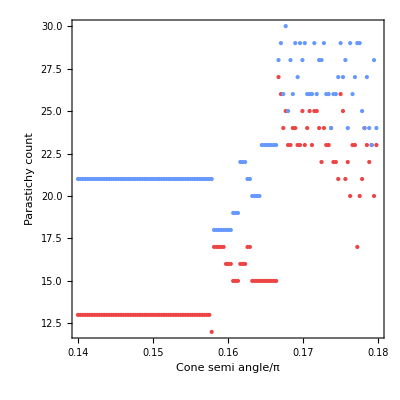

```mathematica
(*thetas=Range[π * 0.14,π*0.18 ,0.001];
Print[Length[thetas]]
arenas2=MapIndexed[ criticalConeArena[First[#2],#1,55]&,thetas];
runs2=Map[doParameterisedRun,arenas2];
Export["runs2.mx",runs2];
*)
runs2=Import["runs2.mx"]
coneThreshold1= Graphics[Map[finalParastichyPoints,runs2],AspectRatio->1,Axes->True,AxesOrigin->{0.1,0}];
jCRExample = Show[coneThreshold1,
FrameLabel->{"Cone semi angle/π","Parastichy count"}
,Frame->True
,BaseStyle->{FontFamily->"Perpetua"},PlotRange->{{0.14,0.18},Automatic}];
jExport[jCRExample]
```

Run  Fibonacci  523 	72.9658	36 	<|Up -> 13, Down -> 21|> 	Elapsed 16 s	Timing 16

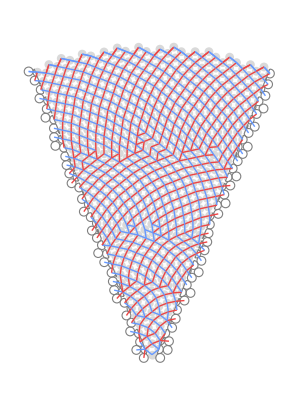

Disk[{0,0},58.3568,{1.09956,2.04204}]

```mathematica
fibonacciArena= criticalConeArena["Fibonacci",0.12 π,55];
fibonacciRun=doParameterisedRun[fibonacciArena];
fibonacciRun=extendRegion[fibonacciRun];
jCRFibonacci= displayConeRun[fibonacciRun];
jExport[jCRFibonacci]
```

```mathematica
jCRFibonacci= displayConeRun[fibonacciRun];
jExport[jCRFibonacci]
```

```mathematica
extendDR[Disk[xy_,r_,sector_]] := Disk[xy,r+2,sector];
extendRegion[run_] := Module[{res=run,dr},
dr=run["Arena"]["DisplayRegion"];
res["Arena"]["DisplayRegion"]=extendDR[dr];
res
]
```

```mathematica
intermediateArena= criticalConeArena["Fibonacci",0.166 π,55];
intermediateRun=doParameterisedRun[intermediateArena];
intermediateRun=extendRegion[intermediateRun];
```

Run  Fibonacci  420 	52.7325	40 	<|Up -> 23, Down -> 15|> 	Elapsed 12 s	Timing 16

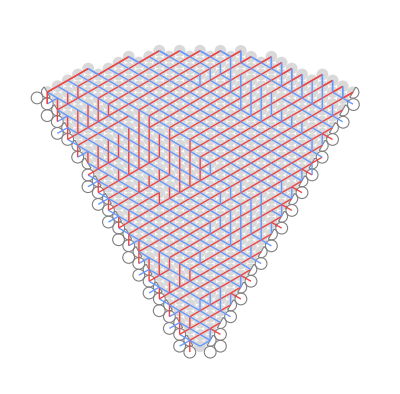

```mathematica
jCRIntermediate= displayConeRun[intermediateRun];
jExport[jCRIntermediate]
```

```mathematica
endArena= criticalConeArena["End",0.175 π,55];
endRun=doParameterisedRun[endArena];
endRun=extendRegion[endRun];
jCREnd= displayConeRun[endRun];
jExport[jCREnd]
```

Run  Test  3000 	170.598	91 	<|Up -> 34, Down -> 55|> 	Elapsed 416 s	Timing 328

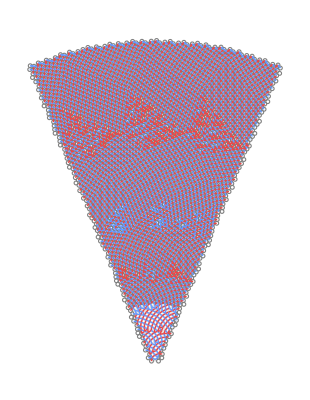

```mathematica
arena3000=testConeArena[3000];
arena3000["Monitoring"]=True;
run3000=doParameterisedRun[arena3000];
(*Export["run3000.mx",run3000];*)
```

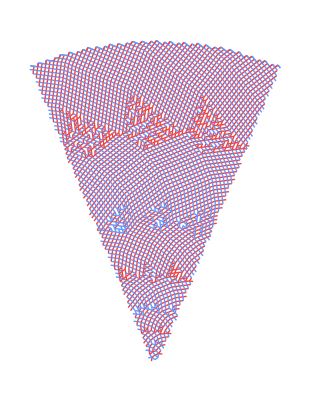

```mathematica
lineConeRun[run3000]
```

```mathematica
Export["run3000.mx",run3000]
```

run3000.mx

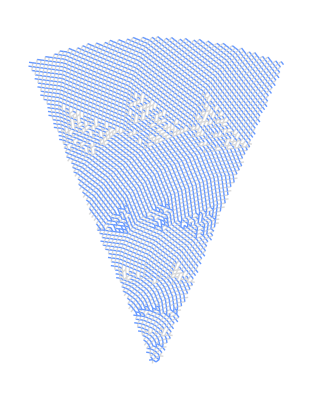

6.0241

```mathematica
jCRLongTerm =Graphics[makeLines[run3000]/. {StandardRed->LightGray}];
jExport[jCRLongTerm]
```

## Display

```mathematica
makeLine[run_,p_ <-> q_ , orientation_] :=  Module[{},
{orientationStyle[orientation],Line[{loggedDiskCentre[run,p],loggedDiskCentre[run,q]}]}
];


makeLines[run_] :=  Module[{chains,diskCentres},
chains=run["Logging"]["ChainStore"];
edgeSet=Join@@Flatten[Map[chainEdges[run,#]&,chains]];
KeyValueMap[makeLine[run,#1,#2]&,edgeSet]
];

makeTopChainLine[run_] :=  Module[{chains,diskCentres},
chains=Take[run["Logging"]["ChainStore"],-1];
edgeSet=Join@@Flatten[Map[chainEdges[run,#]&,chains]];
KeyValueMap[makeLine[run,#1,#2]&,edgeSet]
];
```

```mathematica
displayCone[arena_,rMinMax_] := Module[{xMin,xMax,zMin,zMax},
{xMin,xMax}=rMinMax*Sin[arena["ConeSemiAngle"]];
{zMin,zMax}=rMinMax*Cos[arena["ConeSemiAngle"]];
{{FaceForm[LightGreen],arena["DisplayRegion"]},
Line[{{xMin,zMin},{xMax,zMax}}]
,Line[{{-xMin,zMin},{-xMax,zMax}}]
,Circle[{0,0},rMinMax[[1]],{π/2-arena["ConeSemiAngle"],π/2+arena["ConeSemiAngle"]}]
,Circle[{0,0},rMinMax[[2]],{π/2-arena["ConeSemiAngle"],π/2+arena["ConeSemiAngle"]}]
}
];
```

```mathematica
lom[x_] := If[MissingQ[x],{},x];
labelledDisk[disk_] := {disk["Disk"],Text[disk["ID"],diskCentre[disk["Disk"]]]}
unlabelledDisk[disk_] := {disk["Disk"]}
tooltipDisk[disk_] := Tooltip[disk["Disk"],disk["ID"]];
```

```mathematica
emptyRegionQ[reg_] := Head[reg]===EmptyRegion;
regionDifferencer[region1_,region2_] := Module[{difference},
difference=RegionDifference[region1,region2];
If[Head[difference]==BooleanRegion,
	(* intersection did not work, hopefully because near to tangent *)
	difference=RegionDifference[DiscretizeRegion[region1],DiscretizeRegion[region2]]
];
difference 
];
regionIntersecter[region1_,region2_] := Module[{intersection},
intersection=RegionIntersection[region1,region2];
If[Head[intersection]==BooleanRegion,
	(* intersection did not work, hopefully because near to tangent *)
	intersection=RegionIntersection[DiscretizeRegion[region1],DiscretizeRegion[region2]]
];
intersection
];

diskInsideArenaQ[run_,disk_] :=
emptyRegionQ@ RegionWithin[run["Arena"]["DisplayRegion"],disk];
diskDisjointArenaQ[run_,disk_] := RegionDisjoint[
run["Arena"]["DisplayRegion"],disk];



diskPortionOutsideArena[run_,disk_Disk] := Module[{res},
If[diskInsideArenaQ[run,disk],Return[EmptyRegion[2]]];
If[RegionDisjoint[run["Arena"]["DisplayRegion"],disk],Return[disk]];
res=regionDifferencer[disk,run["Arena"]["DisplayRegion"]];
res
];


diskPortionInsideArena[run_,disk_Disk] := Module[{res},
If[diskInsideArenaQ[run,disk],Return[disk]];
If[diskDisjointArenaQ[run,disk],Return[EmptyRegion[2]]]; (* bug for adjoining regions *)

res=regionIntersecter[disk,run["Arena"]["DisplayRegion"]];
(*If[Head[res]==BooleanRegion,res=CanonicalizePolygon@DiscretizeRegion[res]
];
*)
res
]
```

```mathematica
diskNonIntersectingCylinderQ[run_,disk_Disk] := Module[{},
(
diskCentre[disk][[1]] >= run["Arena"]["CylinderCircumference"]/2+run["Arena"]["DiskRadius"]
||
 diskCentre[disk][[1]]<= -run["Arena"]["CylinderCircumference"]/2
-run["Arena"]["DiskRadius"])
];
diskNonIntersectingConeQ[run_,disk_Disk] := Module[{polar},
polar=disk2Polar[disk];
(
(
polar["θ"] >= run["Arena"]["ConeSemiAngle"]
&& RegionDistance[disk,run["Arena"]["Edges"]["Left"]]> run["Arena"]["DiskRadius"])
||
 diskCentre[disk][[1]]<= -run["Arena"]["CylinderCircumference"]/2
-run["Arena"]["DiskRadius"])
];
```

```mathematica
diskPortionInsideArena[run_,disk_Association] := diskPortionInsideArena[run,disk["Disk"]];
diskPortionOutsideArena[run_,disk_Association] := diskPortionOutsideArena[run,disk["Disk"]];
```

```mathematica
diskClassify[run_] := Module[{},

disks=Values[run["Logging"]["Disks"]];
leftEdgeDisks=leftShift[run["Arena"],#]&/@Select[disks,NumberQ[#ID]&& TrueQ[#CanSupportDisk["Right"]]&];
rightEdgeDisks=rightShift[run["Arena"],#]&/@Select[disks,NumberQ[#ID]&&TrueQ[#CanSupportDisk["Left"]]&];
visibleDisks=Join[
Select[disks,NumberQ[#ID]&],
leftEdgeDisks,
rightEdgeDisks];


croppedDisks=Map[Append[#,
<|
"Cropped"->diskPortionInsideArena[run,#],
"Exterior"->diskPortionOutsideArena[run,#]
|>
]&,visibleDisks];

If[TrueQ[globalShowNumbers],
	numbers=Map[Text[#ID,diskCentre[#Disk]]&,disks],numbers={}];


rimStyle=EdgeForm[Gray];

{{FaceForm[LightGray],EdgeForm[None],#Cropped&/@croppedDisks}
,{FaceForm[None],rimStyle,#Exterior &/@croppedDisks},
numbers
}

];
```

```mathematica
lineConeRun[run_]:=Module[{lines,topChainLines,disks,styledDisks,rMinMax},
disks= Values@run["Logging"]["Disks"];
rMinMax=MinMax[Map[#Polar["r"]&,disks]];
rMinMax=rMinMax+{-run["Arena"]["DiskRadius"],run["Arena"]["DiskRadius"]};
xMax=rMinMax[[2]]* Sin[run["Arena"]["ConeSemiAngle"]]+run["Arena"]["DiskRadius"];

styledDisks= diskClassify[run];

lines=makeLines[run];
topChainLines=makeTopChainLine[run];


graphics=
{
lines,
Thick,topChainLines
(*displayDiskNumbers[arena,disks,Keys[disks]]
*)
};

Show[Graphics[graphics]
,PlotRange->{{-xMax,xMax},rMinMax+{-run["Arena"]["DiskRadius"],run["Arena"]["DiskRadius"]}}]
]
```

```mathematica
displayConeRun[run_]:=Module[{lines,topChainLines,disks,styledDisks,rMinMax},
disks= Values@run["Logging"]["Disks"];
rMinMax=MinMax[Map[#Polar["r"]&,disks]];
rMinMax=rMinMax+{-run["Arena"]["DiskRadius"],run["Arena"]["DiskRadius"]};
xMax=rMinMax[[2]]* Sin[run["Arena"]["ConeSemiAngle"]]+run["Arena"]["DiskRadius"];

styledDisks= diskClassify[run];

lines=makeLines[run];
topChainLines=makeTopChainLine[run];


graphics=
{
(*displayCone[run["Arena"],rMinMax],
*){styledDisks},
lines,
Thick,topChainLines
(*displayDiskNumbers[arena,disks,Keys[disks]]
*)
};

Show[Graphics[graphics]
,PlotRange->{{-xMax,xMax},rMinMax+{-run["Arena"]["DiskRadius"],run["Arena"]["DiskRadius"]}}]
]
```

```mathematica
displayDiskNumbers[arena_,disks_,diskIDs_]:={ EdgeForm[{Thin,Gray}],FaceForm[Lighter[Blue,0.98]],
Map[displayDiskNumber[arena,disks,#]&,diskIDs]
};

displayDiskNumber[arena_,disks_,diskID_]:= Module[{disk},
disk=Lookup[disks,diskID]["Disk"];
{Text[diskID,diskCentre[disk]]}
];

segment[arena_,polar_] := Circle[{0,0},polar["r"],{π/2-1.5 arena["ConeSemiAngle"],π/2+1.5 arena["ConeSemiAngle"]}];
```

## Printout to scale

```mathematica
testScale[] := Module[{},
imageSizeInPoints=20*28.35;
g=testRun[15];
scale=Show[g,Graphics[{Thick,Black,Line[{{1,1},{2,1}}]}],Axes->True,PlotRange->{{-10,10},{0,29}}];
Export["graphic.pdf",g,ImageSize->imageSizeInPoints]
]
```